```mathematica
D[(1-(1-z)b)^n, {z, m}]
```

b^m (1-b (1-z))^(-m+n) FactorialPower[n,m]

```mathematica
Clear[ntot];
KT = 414/100;
k0=1;
eta[ka_, kb_]:=ka / (ka + kb);
koff[eb_, xb_, f_]:= (10^3)Exp[-eb + f xb / KT];
lmd[i_, f_, eb_, ea_]:=1000i*(Exp[-ea+f*(3/2)/(i*KT)]+Exp[-eb+f*2/(i*KT)])
tmean[eb_, ea_,  f_,n_]:=Sum[1/lmd[i, f, eb, ea], {i, 1, n}]
```

```mathematica
Clear[Pm, mAve];
Pm[m_, t_, eb_,ea_, nc_]:=Module[{xa=1.5, xb=2.0, f=0},
koffAPC = koff[ea, xa, f];
koffb = koff[eb, xb, f];
a = koffb + koffAPC;
If[t==0,If[m==nc, 1, 0],
Exp[-a t m](1- Exp[-a t])^(nc-m)FactorialPower[nc, m]/Factorial[m]
]]

mAve[t_, eb_,ea_, nc_]:=Sum[m Pm[m, t, eb, ea, nc], {m, 0, nc}]
```

```mathematica
mAve[1, 10, 10, 20]
```

18.264

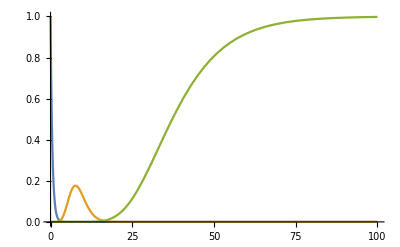

```mathematica
Plot[{
Pm[20, tx, 10, 20],
Pm[10, tx, 10, 20],
Pm[0, tx, 10, 20]
}, {tx,0, 100}, PlotRange->All]
```

```mathematica
Clear[fisherInfo, fisherInfo2]
fisherInfo[t_, eb_, nc_]:=Module[{xa=1.5, xb=2.0, ea=10, f=0},
koffAPC = koff[ea, xa, f];
koffb = koff[eb, xb, f];
a = koffb + koffAPC;
etaT= Exp[-a t];
Sum[Binomial[nc, mx] etaT^mx (1-etaT)^(nc-mx-2) koffb^2 t^2 (nc * etaT - mx)^2, {mx,0, nc}]
]

fisherInfo2[t_, eb_, ea_, nc_]:=Module[{xa=1.5, xb=2.0, f=0},
koffAPC = koff[ea, xa, f];
koffb = koff[eb, xb, f];
a = koffb + koffAPC;
nc koffb^2 t^2 Exp[-a t]/ (1-Exp[-a t])
]
fisherInfo[50, 10, 20]*1.0
fisherInfo2[50, 10,10, 20]*1.0
```

1.11185

1.11185

```mathematica
directComp = {{5.,0.14722922680779657},{5.5,0.24094960649251818},{6.,0.3924762643184822},{6.5,0.6344489894413705},{7.,1.0132352800115079},{7.5,1.5877756988011107},{8.,2.4177329114856967},{8.5,3.532512366963573},{9.,4.883475391177119},{9.5,6.313801384728988},{10.,7.602829514126832},{10.5,8.58198415043295},{11.,9.216755729972947},{11.5,9.579653581387882},{12.,9.770861695659962},{12.5,9.867957197581195},{13.,9.917252586931259},{13.5,9.94287749871608},{14.,9.903426581325832},{14.5,9.93831405890373},{15.,9.957325162781569},{15.5,9.966605498450196},{16.,9.970943314293777}};
```

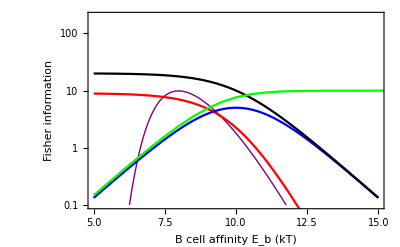

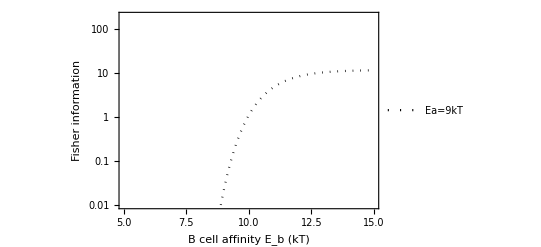

```mathematica
Show[
LogPlot[
{
fisherInfo2[5, ebx, 10,20],
(*fisherInfo2[50, ebx, 10, 20],
fisherInfo2[100, ebx, 10, 20]*)
}, {ebx, 5, 15},
PlotRange->{0.1, 200},
PlotStyle->{{Purple, Thick}, {Purple, Dashed}, {Purple, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"B cell affinity E_b (kT)", "Fisher information"}
],

LogPlot[
Log[20]^2/(1+Exp[eb-10])^2, {eb, 5, 15}, PlotStyle->Red],
LogPlot[
20 * Exp[eb-10]/(1+Exp[eb-10])^2, {eb,5,15}, PlotStyle->Blue
],
LogPlot[
20 /(1+Exp[eb-10]), {eb,5,15}, PlotStyle->Black
],
ListLogPlot[directComp, Joined->True, PlotStyle->Green]

]
```

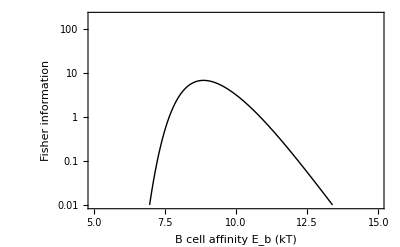

```mathematica
LogPlot[
{
(*fisherInfo2[10, ebx- 2.0*0.5/KT,  9- 1.5*0.5/KT, 20],*)
fisherInfo2[10, ebx- 2.0*0.5/KT, 10- 1.5*0.5/KT, 20]
(*fisherInfo2[10, ebx- 2.0*0.5/KT, 200- 1.5*0.5/KT, 20]*)
}, {ebx, 5, 15},
PlotRange->{0.01, 200},
PlotStyle->{{Black, Thick}, {Black, Dashed}, {Black, Thick}},
Frame->True,
(*PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.8, 0.8}],*)
FrameStyle->Directive[14],
FrameLabel->{"B cell affinity E_b (kT)", "Fisher information"}
]
```

```mathematica
LogPlot[
{
fisherInfo2[50, ebx,  9],
fisherInfo2[50, ebx, 10],
fisherInfo2[50, ebx, 15]
}, {ebx, 5, 15},
PlotRange->{0.01, 200},
PlotStyle->{{Purple, Dotted}, {Purple, Dashed}, {Purple, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"B cell affinity E_b (kT)", "Fisher information"}
]
```

```mathematica
D[t^2 Exp[-b t]/(1-Exp[- b t]), t]
```

(2 ⅇ^(-b t) t)/(1-ⅇ^(-b t))-(b ⅇ^(-2 b t) t^2)/((1-ⅇ^(-b t))^2)-(b ⅇ^(-b t) t^2)/(1-ⅇ^(-b t))

```mathematica
Solve[(2 ⅇ^(-b t) t)/(1-ⅇ^(-b t))-(b ⅇ^(-2 b t) t^2)/((1-ⅇ^(-b t))^2)-(b ⅇ^(-b t) t^2)/(1-ⅇ^(-b t))==0, t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→(2+ProductLog[-2/ⅇ^2])/b}}

```mathematica
2.0+ProductLog[-2/ⅇ^2]
```

1.59362

```mathematica
t^2 Exp[-b t]/(1-Exp[- b t]) /.t->(2+ProductLog[-2/ⅇ^2])/b
```

(ⅇ^(-2-ProductLog[-2/ⅇ^2]) (2+ProductLog[-2/ⅇ^2])^2)/(b^2 (1-ⅇ^(-2-ProductLog[-2/ⅇ^2])))

```mathematica
Simplify[%]
```

((2+ProductLog[-2/ⅇ^2])^2)/(b^2 (-1+ⅇ^(2+ProductLog[-2/ⅇ^2])))

```mathematica
FullSimplify[%]
```

-(ProductLog[-2/ⅇ^2] (2+ProductLog[-2/ⅇ^2]))/b^2

```mathematica
ProductLog[-2.0/ⅇ^2] (2+ProductLog[-2/ⅇ^2])
```

-0.64761

```mathematica
Clear[a, b]
DSolve[y'[x]== a Exp[-a x]-b y[x], y[x], x]
```

```mathematica
Series[kb^2 t^2 Exp[-( kb)t]/(1-Exp[-(kb)t]),{kb, 0, 3}]
```

t kb-(t^2 kb^2)/2+(t^3 kb^3)/12+O[kb]^4

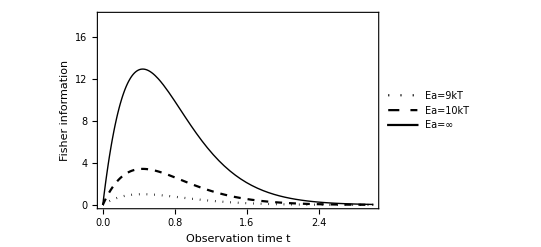

```mathematica
Plot[
{
fisherInfo2[tx *tmean[10- 2.0*0.5/KT, 9-1.5*0.5/KT, 0, 20], 10 - 2.0*0.5/KT,  9- 1.5*0.5/KT, 20],
fisherInfo2[tx*tmean[10- 2.0*0.5/KT, 10-1.5*0.5/KT, 0, 20], 10- 2.0*0.5/KT, 10- 1.5*0.5/KT, 20],
fisherInfo2[tx*tmean[10- 2.0*0.5/KT, 200-1.5*0.5/KT, 0, 20], 10- 2.0*0.5/KT,200- 1.5*0.5/KT, 20]
}, {tx, 0, 3},
PlotRange->{{0, 3},{0, 18}},
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.7, 0.8}],
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Fisher information"}
]
```

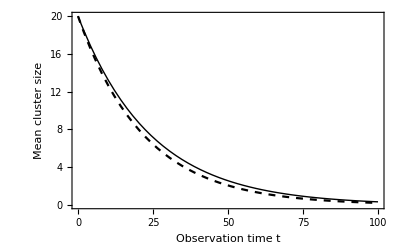

```mathematica
Plot[
{
mAve[tx, 10,  200, 20],
mAve[tx, 10.1, 200, 20]
(*mAve[tx, 10,200, 20]*)
}, {tx, 0, 100},
PlotRange->{0, 20},
PlotStyle->{ {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Mean cluster size"}
]
```

## Coupled ODE

```mathematica
Clear[PmF, nc]
PmF[m_, t_, eb_, f_, ea_, nc_]:=Module[{xa=3/2, xb=2},
Clear[fa, fb, koffAPC, koffb];
fa= f*xa / KT;
fb = f * xb / KT;
koffAPC = koff[ea, xa, 0];
koffb = koff[eb, xb, 0];
Clear[a, ret];
a[n_]:=n*koffAPC*Exp[fa / n] + n * koffb * Exp[fb/n];
If[m==nc, 
ret=Exp[-a[m]t]
,{
If[m>0,
ret = Product[a[i], {i, m+1, nc}]*Sum[ (Exp[(a[m]-a[i])t] - 1)/(Product[(a[j] - a[i]), {j, m, i-1}]Product[(a[j]-a[i]),{j, i+1, nc}]), {i, m+1, nc}]Exp[-a[m]t],
ret= Product[a[i], {i, 1, nc}]*Sum[ (-(Exp[-a[i]t]-1)/a[i] + (Exp[-a[1]t]-1)/a[1])/(Product[(a[j] - a[i]), {j, 1, i-1}]Product[(a[j]-a[i]),{j, i+1, nc}]), {i, 2, nc}]
];}];
ret

]

mAveF[t_, eb_, f_, ea_, nc_]:=Sum[m PmF[m, t,eb,f,ea, nc],{m, 0, nc}]

PmFInfEa[m_, t_, eb_, f_, nc_]:=Module[{ xb=2},
Clear[fa, fb, koffAPC, koffb];
fb = f * xb / KT;
koffb = koff[eb, xb, 0];
Clear[a, ret];
a[n_]:= n * koffb * Exp[fb/n];
If[m==nc, 
ret=Exp[-a[m]t]
,{
If[m>0,
ret = Product[a[i], {i, m+1, nc}]*Sum[ (Exp[(a[m]-a[i])t] - 1)/(Product[(a[j] - a[i]), {j, m, i-1}]Product[(a[j]-a[i]),{j, i+1, nc}]), {i, m+1, nc}]Exp[-a[m]t],
ret= Product[a[i], {i, 1, nc}]*Sum[ (-(Exp[-a[i]t]-1)/a[i] + (Exp[-a[1]t]-1)/a[1])/(Product[(a[j] - a[i]), {j, 1, i-1}]Product[(a[j]-a[i]),{j, i+1, nc}]), {i, 2, nc}]
];}];
ret

]

mAveFInfEa[t_, eb_, f_,  nc_]:=Sum[m PmFInfEa[m, t,eb,f, nc],{m, 0, nc}]
```

```mathematica
N[PmF[0, 20, 10, 10, 200, 20], 9]
N[PmFInfEa[0,20, 10, 10, 20], 9]
```

0.247203924

0.247203924

```mathematica
Pm[0, 20, 10, 20]
```

0.0286995

```mathematica
Sum[PmF[mi, 20, 10, 0, 10, 30], {mi, 0, 30}]
```

1.

```mathematica
PmF[20, 5, 10, 4, 10, 20]
```

0.0000511003

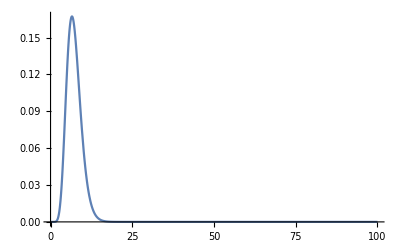

```mathematica
Plot[PmF[10, tx, 10, 5, 10, 20],{tx,0, 100}, PlotRange->All]
```

### Fisher information

```mathematica
Clear[q, fisherInfoF]
```

```mathematica
fisherInfoF[t_, eb_, ea_, f_, nc_]:=Module[{xaF=3/2, xbF=2},
Clear[q, dPdE,faF,fbF,koffAPCF, koffbF];
q[m_]:=koff[eb, xbF, f/m] / (koff[ea, xaF, f/m] + koff[eb, xbF, f/m]);
faF= f*xaF / KT;
fbF = f * xbF / KT;
koffAPCF = koff[ea, xaF, 0];
koffbF = koff[eb, xbF, 0];
Clear[aF];
aF[n_]:=n*koffAPCF*Exp[faF / n] + n * koffbF * Exp[fbF/n];

dPdE[m_]:= -Sum[q[i], {i, m+1, nc}]PmF[m, t, eb, f, ea, nc] + (Product[aF[i], {i, m+1, nc}])Sum[
(
aF[i]q[i]t Exp[-aF[i]t] - aF[m]q[m]t Exp[-aF[m]t] + (Exp[-aF[i]t]-Exp[-aF[m]t]) (Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]),{k, m, i-1}] + Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]),{k, i+1, nc}])
)/(
Product[aF[j]-aF[i], {j, m, i-1}] * Product[aF[j]-aF[i], {j, i+1, nc}]
)
, {i, m+1, nc}];


dPdE0 =-Sum[q[i], {i,1,nc}]PmF[0, t,eb,f,ea, nc] +(Product[aF[i], {i, 1, nc}])Sum[
(
-q[i](1+aF[i]t)Exp[-aF[i]t]/aF[i]+q[i]/aF[i] +q[1](1+aF[1]t)Exp[-aF[1]t]/aF[1]-q[1]/aF[1]+(-(Exp[-aF[i]t]-1)/aF[i] + (Exp[-aF[1]t]-1)/aF[1])(
Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]), {k, 1, i-1}]+Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]), {k, i+1, nc}]
)
)/(Product[(aF[j] - aF[i]), {j, 1, i-1}]*Product[(aF[j]-aF[i]),{j, i+1, nc}])
, {i,2, nc}];

(*Print["dPdE0=", dPdE0 ];
Print["P[0]=", PmF[0, t,eb,f,ea, nc] ];
Print["dPdE1=", dPdE[1]];
Print["P[1]=", PmF[1,t,eb,f,ea, nc]];
Print["part1=", dPdE0^2 / PmF[0, t,eb,f,ea, nc]];
Print["part2=", Sum[(dPdE[m])^2 / PmF[m, t, eb, f, ea, nc] , {m, 1, nc-1}]];
Print["part3=",PmF[nc, t, eb,f,ea, nc]*(aF[nc]*t*q[nc])^2 ];*)
dPdE0^2 / PmF[0, t,eb,f,ea, nc]+Sum[(dPdE[m])^2 / PmF[m, t, eb     , f, ea, nc] , {m, 1, nc-1}] + PmF[nc, t, eb,f,ea, nc]*(aF[nc]*t*q[nc])^2
]
Print["Actual:   ", N[fisherInfoF[50, 10, 10, 0, 20], 9]]
Print["Expected: ", fisherInfo2[50, 10, 10, 20]]
```

Actual:   1.11185158

Expected: 1.11185

```mathematica
fisherInfoFInfEa[t_, eb_, f_, nc_]:=Module[{xbF=2},
Clear[q, dPdE,faF,fbF,koffAPCF, koffbF];
q[m_]:=1;
fbF = f * xbF / KT;
koffbF = koff[eb, xbF, 0];
Clear[aF];
aF[n_]:= n * koffbF * Exp[fbF/n];

dPdE[m_]:= -Sum[q[i], {i, m+1, nc}]PmFInfEa[m, t, eb, f, nc] + (Product[aF[i], {i, m+1, nc}])Sum[
(
aF[i]q[i]t Exp[-aF[i]t] - aF[m]q[m]t Exp[-aF[m]t] + (Exp[-aF[i]t]-Exp[-aF[m]t]) (Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]),{k, m, i-1}] + Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]),{k, i+1, nc}])
)/(
Product[aF[j]-aF[i], {j, m, i-1}] * Product[aF[j]-aF[i], {j, i+1, nc}]
)
, {i, m+1, nc}];


dPdE0 =-Sum[q[i], {i,1,nc}]PmFInfEa[0, t,eb,f, nc] +(Product[aF[i], {i, 1, nc}])Sum[
(
-q[i](1+aF[i]t)Exp[-aF[i]t]/aF[i]+q[i]/aF[i] +q[1](1+aF[1]t)Exp[-aF[1]t]/aF[1]-q[1]/aF[1]+(-(Exp[-aF[i]t]-1)/aF[i] + (Exp[-aF[1]t]-1)/aF[1])(
Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]), {k, 1, i-1}]+Sum[(aF[k]q[k]-aF[i]q[i])/(aF[k]-aF[i]), {k, i+1, nc}]
)
)/(Product[(aF[j] - aF[i]), {j, 1, i-1}]*Product[(aF[j]-aF[i]),{j, i+1, nc}])
, {i,2, nc}];

(*Print["dPdE0=", dPdE0 ];
Print["P[0]=", PmF[0, t,eb,f,ea, nc] ];
Print["dPdE1=", dPdE[1]];
Print["P[1]=", PmF[1,t,eb,f,ea, nc]];
Print["part1=", dPdE0^2 / PmF[0, t,eb,f,ea, nc]];
Print["part2=", Sum[(dPdE[m])^2 / PmF[m, t, eb, f, ea, nc] , {m, 1, nc-1}]];
Print["part3=",PmF[nc, t, eb,f,ea, nc]*(aF[nc]*t*q[nc])^2 ];*)
dPdE0^2 / PmFInfEa[0, t,eb,f, nc]+Sum[(dPdE[m])^2 / PmFInfEa[m, t, eb     , f,  nc] , {m, 1, nc-1}] + PmFInfEa[nc, t, eb,f, nc]*(aF[nc]*t*q[nc])^2
]
Print["Actual:   ", fisherInfoFInfEa[50, 10, 0, 20]*1.0]
Print["Expected: ", fisherInfo2[50, 10, 200, 20]*1.0]

Print["Actual:   ", fisherInfoFInfEa[50, 10, 5, 20]*1.0]
Print["Expected: ", fisherInfoF[50, 10, 200, 5, 20]*1.0]
```

Actual:   11.8739

Expected: 11.8739

Actual:   6.39706

Expected: 6.39706

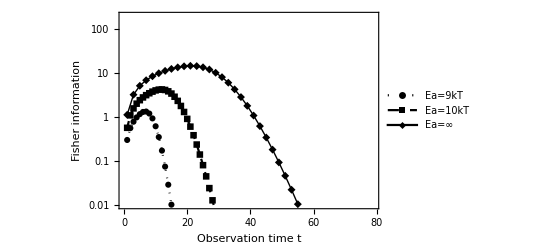

```mathematica
Show[ListLogPlot[
{
Table[{tx, N[fisherInfoF[tx, 10,  9, 10, 20], 5]}, {tx, 1, 20, 1}],
Table[{tx, N[fisherInfoF[tx, 10,  10, 10, 20], 5]}, {tx, 1, 40, 1}],
Table[{tx, N[fisherInfoFInfEa[tx, 10,  10, 20], 5]}, {tx, 1, 80, 2}]
}, 
PlotRange->{0.01, 200},
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
PlotMarkers->Automatic,
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Fisher information"}
]

]
```

```mathematica
FIvsTo = {
Table[{tx, N[fisherInfoF[tx, 10,  9, 10, 20], 5]}, {tx, 1, 20, 1}],
Table[{tx, N[fisherInfoF[tx, 10,  10, 10, 20], 5]}, {tx, 1, 40, 1}],
Table[{tx, N[fisherInfoFInfEa[tx, 10,  10, 20], 5]}, {tx, 1, 80, 2}]
};
```

```mathematica
FIvsTo2 = {
Table[{tx / tmean[10, 9, 10, 20], N[fisherInfoF[tx, 10,  9, 10, 20], 5]}, {tx, 1, 20, 1}],
Table[{tx/tmean[10, 10, 10, 20], N[fisherInfoF[tx, 10,  10, 10, 20], 5]}, {tx, 1, 40, 1}],
Table[{tx/tmean[10, 200, 10, 20], N[fisherInfoFInfEa[tx, 10,  10, 20], 5]}, {tx, 1, 80, 2}]
};
```

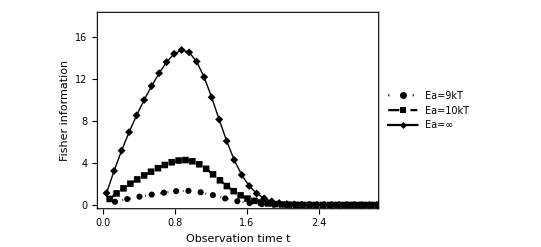

```mathematica
Show[ListPlot[
FIvsTo2, 
PlotRange->{{0, 3}, {0, 18}},
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
PlotMarkers->Automatic,
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Fisher information"}
]

]
```

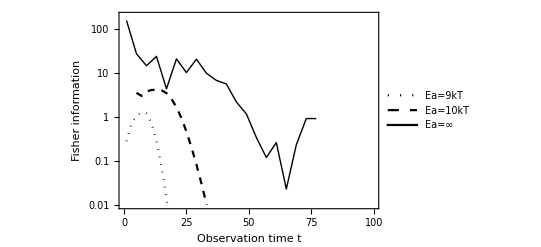

```mathematica
$MaxExtraPrecision = 500;
Show[ListLogPlot[
{
Table[{tx, fisherInfoF[tx, 10,  9, 8, 20]}, {tx, 1, 30, 2}],
Table[{tx, fisherInfoF[tx,10,  10, 8, 20]}, {tx, 1, 40, 2}],
Table[{tx, fisherInfoFInfEa[tx, 10,  8,20]}, {tx, 1, 80, 4}]
}, 
PlotRange->{{0, 100},{0.01, 200}},
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
(*PlotMarkers->Automatic,*)
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Fisher information"}
]

]
```

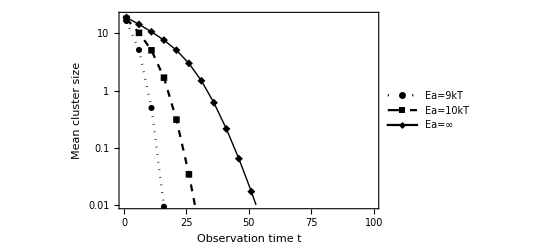

```mathematica
ListLogPlot[
{
Table[{tx, mAveF[tx, 10, 7,  9, 20]}, {tx, 1, 100, 5}],
Table[{tx, mAveF[tx, 10,  7, 10, 20]}, {tx, 1, 100, 5}],
Table[{tx, mAveFInfEa[tx, 10,  7, 20]}, {tx, 1, 100, 5}]
}, 
PlotRange->{{0, 100},{0.01, 20}},
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
PlotMarkers->Automatic,
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Mean cluster size"}
]
```

```mathematica
pdf[50, 20,  7,  10.0]
```

3.906×10^-9

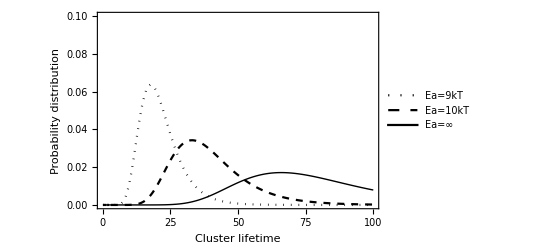

```mathematica
ListPlot[
{
Table[{tx, pdf[tx, 20,  0,  10, 9]}, {tx, 0, 100, 0.5}],
Table[{tx, pdf[tx, 20,   0, 10, 10]}, {tx, 0, 100, 0.5}],
Table[{tx, pdf[tx, 20,   0, 10, 200.0]}, {tx, 0, 100, 0.5}]
}, 
(*PlotRange->{0.01, 20},*)
PlotRange->{0, 0.1},
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
(*PlotMarkers->Automatic,*)
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Cluster lifetime", "Probability distribution"}
]
```

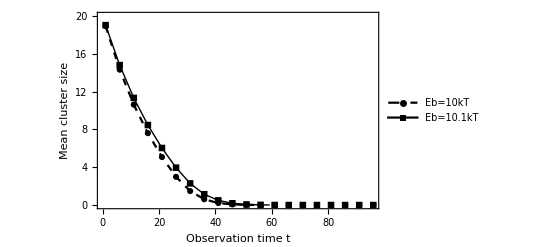

```mathematica
ListPlot[
{
Table[{tx, mAveFInfEa[tx, 10, 7,   20]}, {tx, 1, 100, 5}],
Table[{tx, mAveFInfEa[tx, 10.1,  7,  20]}, {tx, 1, 100, 5}]
(*Table[{tx, mAveFInfEa[tx, 10,  7, 20]}, {tx, 1, 100, 5}]*)
}, 
PlotRange->{0.01, 20},
PlotLegends->Placed[{"Eb=10kT", "Eb=10.1kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
PlotMarkers->Automatic,
PlotStyle->{{Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Observation time t", "Mean cluster size"}
]
```

```mathematica
Table[{ebx}, {ebx, 5, 15, 1/3}]
```

{{5},{16/3},{17/3},{6},{19/3},{20/3},{7},{22/3},{23/3},{8},{25/3},{26/3},{9},{28/3},{29/3},{10},{31/3},{32/3},{11},{34/3},{35/3},{12},{37/3},{38/3},{13},{40/3},{41/3},{14},{43/3},{44/3},{15}}

General::munfl: 6.42122×10^-372 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.07348×10^-368 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 2.28753×10^-366 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

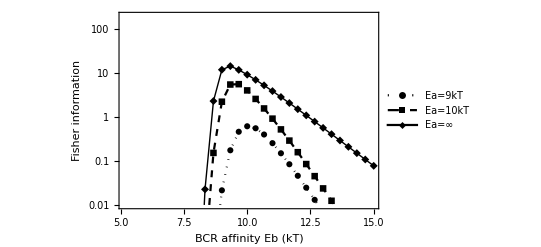

```mathematica
$MaxExtraPrecision = 500;
ListLogPlot[
{
Table[{ebx, N[fisherInfoF[10, ebx,  9, 10, 20],6]}, {ebx, 5, 13, 1/3}],
Table[{ebx, N[fisherInfoF[10, ebx,  10, 10, 20], 6]}, {ebx, 5, 14, 1/3}],
Table[{ebx, N[fisherInfoFInfEa[10, ebx,  10, 20], 6]}, {ebx, 5, 15, 1/3}]
}, 
PlotRange->{0.01, 200},
PlotLegends->Placed[{"Ea=9kT", "Ea=10kT", "Ea=∞"},{0.7, 0.8}],
Joined->True,
PlotMarkers->Automatic,
PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"BCR affinity Eb (kT)", "Fisher information"}
]
```

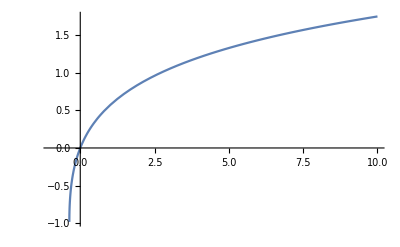

```mathematica
Plot[ProductLog[x], {x, -1, 10}]
```

```mathematica
Series[Exp[-(ka + kb)t]/(1-Exp[-(ka+kb)t]), {kb, 0, 3}]
```

1/(-1+ⅇ^(ka t))-(ⅇ^(ka t) t kb)/((-1+ⅇ^(ka t))^2)+(ⅇ^(ka t) (1+ⅇ^(ka t)) t^2 kb^2)/(2 (-1+ⅇ^(ka t))^3)-((ⅇ^(ka t) (1+4 ⅇ^(ka t)+ⅇ^(2 ka t)) t^3) kb^3)/(6 (-1+ⅇ^(ka t))^4)+O[kb]^4

```mathematica
Solve[2(1.0-Exp[-(0+ kb)t] )== kb t, kb]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{kb→0.},{kb→1.59362/t}}

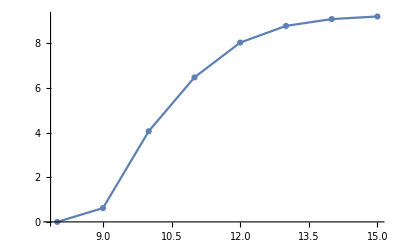

```mathematica
ListPlot[Table[{eax,N[fisherInfoF[10, 10, eax, 10, 20],5]}, {eax, 8, 15}], Joined->True, PlotMarkers->Automatic]
```

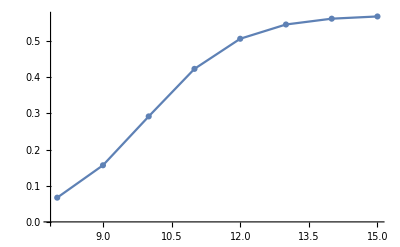

```mathematica
ListPlot[Table[{eax,N[fisherInfoF[1/2, 10, eax, 10, 20],5]}, {eax, 8, 15}], Joined->True, PlotMarkers->Automatic]
```

```mathematica
infoPerCluster0F = Table[{ncx,fisherInfoF[10, 10, 200, 0, ncx]/ncx}, {ncx, 2, 29}]
```

{{2,0.358713},{3,0.358713},{4,0.358713},{5,0.358713},{6,0.358713},{7,0.358713},{8,0.358713},{9,0.358713},{10,0.358713},{11,0.358713},{12,0.358713},{13,0.358713},{14,0.358713},{15,0.358713},{16,0.358713},{17,0.358713},{18,0.358713},{19,0.358713},{20,0.358713},{21,0.358713},{22,0.358712},{23,0.358713},{24,0.358717},{25,0.358703},{26,0.358721},{27,0.358747},{28,0.358685},{29,0.358769}}

```mathematica
N[fisherInfoFInfEa[10, 12, 20, 30],6]/30
```

0.0823932

```mathematica
infoPerClusterE10FInfEaF20 = Table[{ncx, N[fisherInfoFInfEa[10, 10, 20, ncx], 6]/ncx}, {ncx, 2, 50}]
```

{{2,2.49649×10^-46},{3,8.55152×10^-13},{4,4.62805×10^-7},{5,0.0000706572},{6,0.00125338},{7,0.00847305},{8,0.0323296},{9,0.0840775},{10,0.166461},{11,0.270022},{12,0.378176},{13,0.475279},{14,0.551644},{15,0.604238},{16,0.634875},{17,0.647866},{18,0.648169},{19,0.640276},{20,0.627735},{21,0.613074},{22,0.597936},{23,0.58329},{24,0.569633},{25,0.557164},{26,0.545903},{27,0.535782},{28,0.526687},{29,0.518498},{30,0.511099},{31,0.504384},{32,0.498264},{33,0.492661},{34,0.48751},{35,0.482756},{36,0.478354},{37,0.474264},{38,0.470452},{39,0.466891},{40,0.463556},{41,0.460424},{42,0.457478},{43,0.454701},{44,0.452079},{45,0.449598},{46,0.447248},{47,0.445018},{48,0.442898},{49,0.440882},{50,0.438961}}

```mathematica
infoPerClusterE9FInfEaF20 = Table[{ncx,1000 N[fisherInfoFInfEa[10, 9, 20, ncx], 6]/ncx}, {ncx, 2, 50}]
```

{{2,2.22291×10^-127},{3,2.2235×10^-34},{4,2.30665×10^-18},{5,1.06343×10^-12},{6,8.09684×10^-10},{7,5.93246×10^-8},{8,1.42086×10^-6},{9,0.0000175146},{10,0.000138091},{11,0.000787346},{12,0.00350626},{13,0.0128445},{14,0.0401556},{15,0.110077},{16,0.270093},{17,0.602777},{18,1.23928},{19,2.37154},{20,4.26019},{21,7.23484},{22,11.6848},{23,18.039},{24,26.7367},{25,38.1917},{26,52.7544},{27,70.6768},{28,92.0847},{29,116.961},{30,145.143},{31,176.328},{32,210.095},{33,245.93},{34,283.258},{35,321.475},{36,359.98},{37,398.199},{38,435.607},{39,471.743},{40,506.223},{41,538.735},{42,569.05},{43,597.009},{44,622.524},{45,645.566},{46,666.155},{47,684.357},{48,700.27},{49,714.019},{50,725.747}}

```mathematica
infoPerClusterE15FInfEaF20 = Table[{ncx,1000 N[fisherInfoFInfEa[10, 15, 20, ncx], 6]/ncx}, {ncx, 2, 50}]
```

```mathematica
infoPerClusterE12FInfEaF20plus =  Table[{ncx,1000 N[fisherInfoFInfEa[10, 12, 20, ncx], 6]/ncx}, {ncx, 60, 100, 20}]
```

{{60,70.0164},{80,67.2389},{100,65.6278}}

```mathematica
Join[Table[i, {i, 1, 2}], Table[i, {i, 3, 4}]]
```

{1,2,3,4}

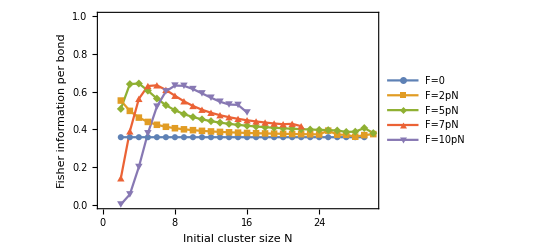

```mathematica
ListPlot[{
infoPerCluster0F,
infoPerCluster2FInfEa,
infoPerCluster5FInfEa,
infoPerCluster7FInfEa,
infoPerCluster10FInfEa
}, Joined->True, PlotMarkers->Automatic, PlotRange->{0, 1},

PlotLegends->Placed[{"F=0", "F=2pN", "F=5pN", "F=7pN", "F=10pN"},{0.8, 0.7}],
(*PlotStyle->{{Black, Dotted}, {Black, Dashed}, {Black, Thick}},*)
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Initial cluster size N", "Fisher information per bond"}
]
```

```mathematica
Length[infoPerClusterE12FInfEaF20]
```

49

```mathematica
Table[{infoPerClusterE12FInfEaF20[[i, 1]], infoPerClusterE12FInfEaF20[[i, 2]]}, {i, 1, Length[infoPerClusterE12FInfEaF20]}]
```

{{2,0.0000246969},{3,0.102254},{4,0.332311},{5,0.39558},{6,0.338987},{7,0.268768},{8,0.218019},{9,0.185072},{10,0.163188},{11,0.147798},{12,0.136386},{13,0.127575},{14,0.120562},{15,0.114847},{16,0.110102},{17,0.106099},{18,0.102678},{19,0.0997204},{20,0.0971394},{21,0.0948675},{22,0.0928525},{23,0.0910535},{24,0.0894377},{25,0.0879785},{26,0.0866544},{27,0.0854475},{28,0.0843429},{29,0.0833283},{30,0.0823932},{31,0.0815285},{32,0.0807266},{33,0.079981},{34,0.079286},{35,0.0786365},{36,0.0780283},{37,0.0774576},{38,0.076921},{39,0.0764156},{40,0.0759386},{41,0.0754879},{42,0.0750613},{43,0.0746568},{44,0.0742729},{45,0.073908},{46,0.0735608},{47,0.0732299},{48,0.0729143},{49,0.0726129},{50,0.0723248}}

```mathematica
infoPerClusterE8FInfEaF20
```

{{2,0.},{3,1.06067×10^-105},{4,9.82885×10^-62},{5,1.24797×10^-46},{6,1.34278×10^-39},{7,1.17554×10^-35},{8,4.45341×10^-33},{9,3.65636×10^-31},{10,1.25669×10^-29},{11,2.4483×10^-28},{12,3.18563×10^-27},{13,3.05868×10^-26},{14,2.31431×10^-25},{15,1.4447×10^-24},{16,7.69366×10^-24},{17,3.58455×10^-23},{18,1.48993×10^-22},{19,5.61108×10^-22},{20,1.9386×10^-21},{21,6.20769×10^-21},{22,1.85802×10^-20},{23,5.23534×10^-20},{24,1.39712×10^-19},{25,3.54946×10^-19},{26,8.62319×10^-19},{27,2.0111×10^-18},{28,4.51785×10^-18},{29,9.80524×10^-18},{30,2.06139×10^-17},{31,4.20781×10^-17},{32,8.35713×10^-17},{33,1.618×10^-16},{34,3.05885×10^-16},{35,5.65532×10^-16},{36,1.02395×10^-15},{37,1.81791×10^-15},{38,3.16838×10^-15},{39,5.42663×10^-15},{40,9.1426×10^-15},{41,1.5165×10^-14},{42,2.47858×10^-14},{43,3.99467×10^-14},{44,6.35299×10^-14},{45,9.97648×10^-14},{46,1.54789×10^-13},{47,2.37414×10^-13},{48,3.60171×10^-13},{49,5.40699×10^-13},{50,8.0361×10^-13}}

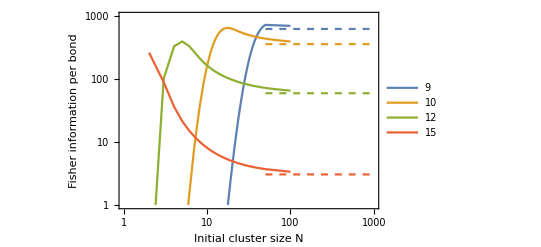

```mathematica
Show[ListLogLogPlot[{
(*infoPerCluster0F,*)
(*Table[{infoPerClusterE8FInfEaF20[[i, 1]], 1000infoPerClusterE8FInfEaF20[[i, 2]]}, {i, 1, Length[infoPerClusterE8FInfEaF20]}],*)
Join[infoPerClusterE9FInfEaF20,infoPerClusterE9FInfEaF20plus],
(*infoPerClusterE9FInfEa,
infoPerClusterE10FInfEa,*)
Join[Table[{infoPerClusterE10FInfEaF20[[i, 1]],1000 infoPerClusterE10FInfEaF20[[i, 2]]}, {i, 1, Length[infoPerClusterE10FInfEaF20]}], infoPerClusterE10FInfEaF20plus],
(*infoPerClusterE11FInfEa,*)
Join[Table[{infoPerClusterE12FInfEaF20[[i, 1]], 1000infoPerClusterE12FInfEaF20[[i, 2]]}, {i, 1, Length[infoPerClusterE12FInfEaF20]}],infoPerClusterE12FInfEaF20plus],
Join[infoPerClusterE15FInfEaF20,infoPerClusterE15FInfEaF20plus]
}, Joined->True,(* PlotMarkers->Automatic,*) PlotRange->{{1, 1000},{1, 1000}},

PlotLegends->Placed[{"9", "10", "12", "15"},{0.9, 0.3}],
(*PlotMarkers->Automatic,*)
(*PlotStyle->{{Purple}, {Blue}, {Green}, {Yellow}, {Red}},*)
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Initial cluster size N", "Fisher information per bond"}
],
LogLogPlot[{
50 fisherInfo2[10, 9, 200, 20],
50 fisherInfo2[10, 10, 200, 20],
50 fisherInfo2[10, 12, 200, 20],
50 fisherInfo2[10, 15, 200, 20]}, {nx, 50, 1000}, PlotStyle->Dashed]
]
```

```mathematica
fisherInfoFInfEa[20, 10, 5, 10]
```

7.23065

```mathematica
fisherInfoF[20, 10, 10, 0, 10]
```

1.60177

General::munfl: Exp[-834.916] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-745.587] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-834.916] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

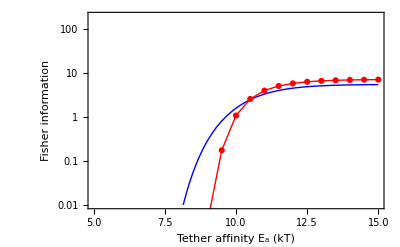

```mathematica
Show[
LogPlot[
{
fisherInfo2[20, 10, ebx, 10]
(*fisherInfo2[50, 10, ebx, 20],
fisherInfo2[50, 10, ebx, 20]*)
}, {ebx, 5, 15},
PlotRange->{0.01, 200},
PlotStyle->{{Blue, Thick}}
],
ListLogPlot[
Table[{eax,fisherInfoF[20, 10, eax, 5, 10]}, {eax, 5, 15, 0.5}],
Joined->True, PlotMarkers->Automatic, PlotStyle->{Red, Thick}
],
Frame->True,
FrameStyle->Directive[14],
FrameLabel->{"Tether affinity E_a (kT)", "Fisher information"}

]
```

## Calculate lower bound

```mathematica
Integrate[n b t e^{-b t} (1-e^{-b t})^(n-1), {t, 0, Infinity}]
```

{∫_0^∞ b e^(-b t) (1-e^(-b t))^(-1+n) n tⅆt}

```mathematica
lifetime[Ea_, Eb_]
```

```mathematica
Plot[]
```

```mathematica
Solve[n b t e^{-b t} (1-Exp[-b t])^(n-1)==0, t]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{t→0},{t→Log[1/(1-0^(1/(-1+n)))]/b}}

```mathematica
D[n b  Exp[-b t] (1-Exp[-b t])^(n-1), t]
```

-b^2 ⅇ^(-b t) (1-ⅇ^(-b t))^(-1+n) n+b^2 ⅇ^(-2 b t) (1-ⅇ^(-b t))^(-2+n) (-1+n) n

```mathematica
Solve[-b^2 ⅇ^(-b t) (1-ⅇ^(-b t))^(-1+n) n+b^2 ⅇ^(-2 b t) (1-ⅇ^(-b t))^(-2+n) (-1+n) n==0, t]
```

{{t→ConditionalExpression[(2 ⅈ π C[1])/b, C[1]∈ℤ&&Re[n]>2]},{t→ConditionalExpression[(2 ⅈ π C[1]+Log[n])/b, C[1]∈ℤ]}}